```mathematica
SetDirectory["C:\\Users\\86177\\Desktop\\502\\v16\\Console1"];
charm276=Import["./charm_dis_276.txt","Table"];
charm502=Import["./charm_dis_502.txt","Table"];
```

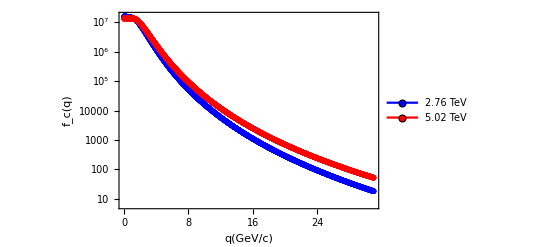

```mathematica
fck=Show[{ListLogPlot[{charm276,charm502},PlotStyle->{Blue,Red},PlotLegends->Placed[{"2.76 TeV","5.02 TeV"},{Right,Top}],PlotMarkers->{{Graphics[{Blue,Disk[]}],0.01},{Graphics[{Red,Disk[]}],0.01}},Joined->True]},
FrameLabel->{"q(GeV/c)","f_c(q)"},
LabelStyle->Directive[Black,Bold,12] ,FrameTicksStyle->{{Black,Thick},{Black,Thick}},Frame->True,FrameStyle->Thick]
```

```mathematica
Export["fck.png",fck,ImageResolution->400]
```

fck.png

```mathematica
SystemOpen[DirectoryName[AbsoluteFileName["fck.png"]]]
```